# Nanobot Theory : Data Analysis and Plotting

#### Yibin Jiang, Abhishek Sharma Cronin Lab University of Glasgow

```mathematica
baseDirectory=NotebookDirectory[];
data = Import[NotebookDirectory[]<>"/1/C_cross_1000000_128_test_normalized_by_r.csv"];
```

```mathematica
wavelength =Table[0.39+0.01*i,{i,41}];
```

```mathematica
plotUVVis[index_]:= Block[{Au,structure,reffi,tempData,intp,plot1,plot2,fig},
tempData=Transpose[{1000*wavelength,data⟦All,1+index⟧}];
intp=Interpolation[tempData,InterpolationOrder->2];
plot1=Plot[intp[x],{x,400,800},PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotRange->{0,12}];
plot2=ListPlot[tempData,PlotStyle->{Black,PointSize[0.02]},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]}];
fig=Show[{plot1,plot2},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame-> True,FrameLabel->{"Wavelength (nm)","Extinction"},AspectRatio->1,ImageSize->300,PlotRange->{0,1.0}];Return[fig]];
```

```mathematica
restylePlot2[p_,op:OptionsPattern[ListLinePlot]]:=ListLinePlot[Cases[Normal@p,Line[x__]:>x,∞],op,Options[p]];
```

```mathematica
Dimensions@data
```

{41,16895}

```mathematica
17000/4
```

4250

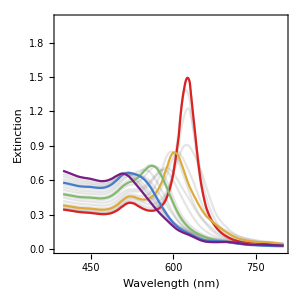

Z:\group\Yibin Jiang\Papers\Nanobot_Theory\Code\Growth_with_silverV3_traj5\/UV_Vis.png

```mathematica
plots = Flatten@{Table[plotUVVis[i],{i,16894,0,-4250}],plotUVVis[0]};
f = restylePlot2[plots,PlotStyle->Reverse@Table[ColorData["Rainbow"][i],{i,0,1,1/(Length[plots]-1)}],FrameStyle->Directive[16,FontColor->Black],PlotRange->{0,2},AspectRatio->1,ImageSize->300,Frame-> True,FrameLabel->{"Wavelength (nm)","Extinction"}];
plots = Flatten@{Table[plotUVVis[i],{i,0,16895,1000}],plotUVVis[16895-1]};
f2 = restylePlot2[plots,PlotStyle->Opacity[0.2,Gray],FrameStyle->Directive[16,FontColor->Black],PlotRange->{0,2},AspectRatio->1,ImageSize->300,Frame-> True,FrameLabel->{"Wavelength (nm)","Extinction"}];
p = Show[{f2,f}]
Export[NotebookDirectory[]<>"/UV_Vis.png",p,ImageResolution->300]
```

```mathematica
Table[i,{i,16894,0,-4250}]
```

{16894,12644,8394,4144}